```mathematica
(*
parameters:;
21 2;
1000 10000 20 1;
*)
```

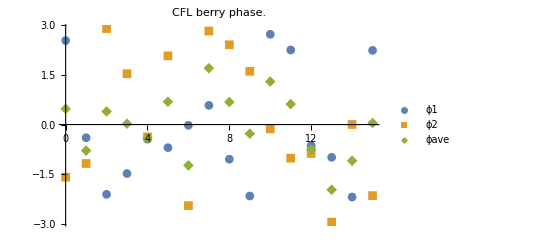

Total Berry Phase mod π:

-0.586463

-0.186677

2.95492

```mathematica
bm1=Import["Google Drive/jie_programs/QHlattice/CFLberryphase/output_21_oned","Table"];
n:=Length[bm1];
x=Table[bm1[[i]][[1]],{i,1,n}];
phase1= Table[{x[[i]],bm1[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm1[[i]][[3]]},{i,1,n}];
phaseave= Total[{phase1,phase2}]/2;

ListPlot[{phase1,phase2,phaseave},PlotLegends->{"ϕ1","ϕ2","ϕave"},PlotMarkers->Automatic, PlotLabel->"CFL berry phase."]

Print["Total Berry Phase mod π:"]
Total[phaseave][[2]]
Total[phaseave][[2]]/π
Mod[%,π]
```

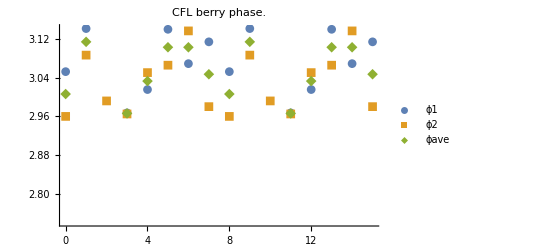

Total Berry Phase mod π:

42.628

13.5689

1.00255

```mathematica
bm2=Import["Google Drive/jie_programs/QHlattice/CFLberryphase/output_21_twod","Table"];
n:=Length[bm2];
x=Table[bm2[[i]][[1]],{i,1,n}];
phase1= Table[{x[[i]],bm2[[i]][[2]]},{i,1,n}];
phase2= Table[{x[[i]],bm2[[i]][[3]]},{i,1,n}];
phaseave= Total[{phase1,phase2}]/2;

ListPlot[{phase1,phase2,phaseave},PlotLegends->{"ϕ1","ϕ2","ϕave"},PlotMarkers->Automatic, PlotLabel->"CFL berry phase."]

Print["Total Berry Phase mod π:"]
Total[phaseave][[2]]
Total[phaseave][[2]]/π
Mod[%,π]
```

```mathematica
π/2//N
```

1.5708